Wolfram Online Mini Campus. Part 11

Instagram Posts
Pinterest Posts
"Translation" of SageMath Online Mini Campus. Part 11

Solutions as Art Objects

```mathematica
EQ[x_,y_]:=x^4-4x^3*y-4x^2y^2+x*y^3+y^4;
PT={x,y}/.FindInstance[EQ[x,y]==1,{x,y},Integers,10];
ContourPlot[EQ[x,y]==1,{x,-5,5},{y,-5,5},
ContourStyle->Dotted,ImageSize->500,
Epilog->{Table[Style[Text[CharacterRange["♔","♟"][[i]],
PT[[i]]],Hue[i/10],Large],{i,10}]}]
```

-Graphics-

```mathematica
RegionPlot[Sin[x^2]Sin[y^2]Sin[x*y]≥.001,
{x,-4,4},{y,-4,4},PlotPoints->100,
BoundaryStyle->{Brown,Dashed},ImageSize->500,
PlotStyle->Texture[ExampleData[{"ColorTexture",
ExampleData["ColorTexture"][[6,2]]}]]]
```

-Graphics-

Graphics as Art Objects

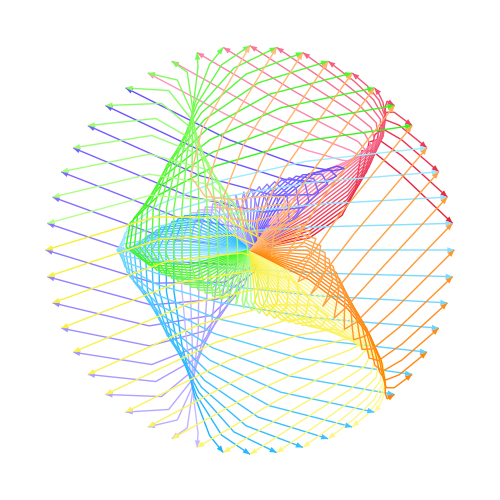

```mathematica
Graphics[Table[{ColorData["BrightBands"][k/108],
Arrowheads[{.005,.005,.02,.025,.03,.035}],
Arrow[BezierCurve[{{0,0},
{Cos[k*Pi/48],Sin[k*Pi/48]},
{Sin[k*Pi/32],Cos[k*Pi/32]},
{Cos[k*Pi/24],Sin[k*Pi/24]}}]]},
{k,108}],ImageSize->500]
```

Graphs as Art Objects

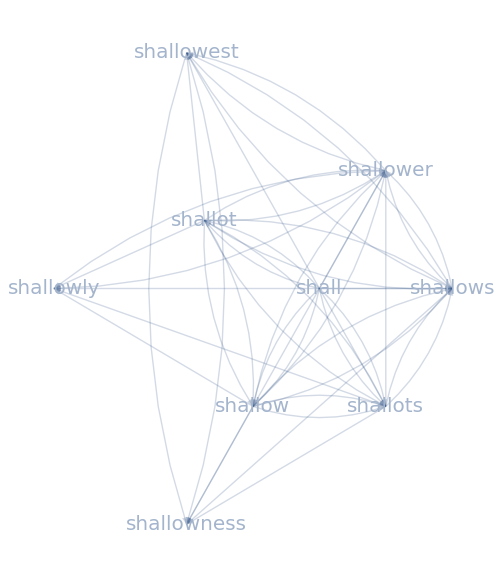

```mathematica
W=Flatten[Map[(Thread[# ->DeleteCases[Nearest[DictionaryLookup["shall*"],
#,6],#]])&,DictionaryLookup["shall*"]]];
GraphPlot[W,VertexShapeFunction->({Text[Style[#2,20,Italic,
Hue[3-#1],Opacity[1]],#1,Background->White]}&),
EdgeShapeFunction->"CarvedArcArrow",EdgeStyle->Opacity[.2],
GraphLayout->"RadialEmbedding",ImageSize->500]
```

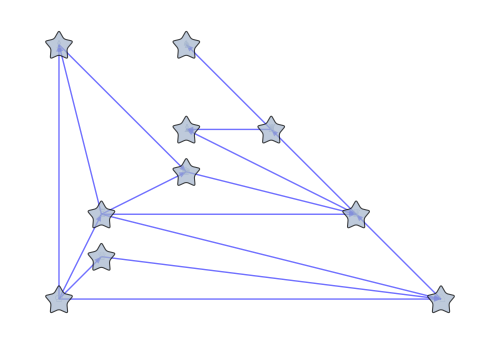

```mathematica
EL={"♔"<->"♕","♔"<->"♖","♔"<->"♗","♔"<->"♘",
"♕"<->"♘","♖"<->"♘","♖"<->"♚","♖"<->"♛",
"♗"<->"♖","♗"<->"♚","♘"<->"♛","♚"<->"♛",
"♛"<->"♜","♛"<->"♝","♜"<->"♝","♜"<->"♞"};
EP={"PlanarEmbedding","StarEmbedding",
"LayeredDigraphEmbedding",Automatic};        
EGP[e_]:=GraphPlot[Graph[EL],GraphLayout->e,
VertexLabels->Placed[Automatic,{.5,.5}],
VertexSize->.6,EdgeStyle->RGBColor["#3636ff"],
VertexStyle->{RGBColor["Silver"],Opacity[0.7]},
VertexShapeFunction->"ConcavePentagon",
EdgeShapeFunction->"CarvedArrow",ImageSize->500];
EGP[EP[[1]]]
```

Spherical Coordinates as Art Objects

```mathematica
SphericalPlot3D[ϕ/3+3Cos[3θ],{θ,0,2Pi},{ϕ,0,2Pi},
PlotPoints->20,ImageSize->500,Mesh->False,Boxed->False,
Axes->False,PlotStyle->Opacity[.2],
ColorFunction->Function[{x,y,z},
ColorData["DeepSeaColors"][Cos[x]-Sin[z]]]]
```

-Graphics3D-

Data Objects

External Files

```mathematica
DC=Import["https://olgabelitskaya.github.io/huge_cities.tsv",
"Dataset", "HeaderLines" -> 1]; DC[1;;5]
PM=Normal[DC[[All,2]]];PC=Values/@Normal[DC[[All,{9,8}]]];
PS=Rescale[Normal[DC[[All,6]]],{2,4}];
TP=Table[Graphics[{ColorData["CandyColors"][i/20],
PointSize[PS[[i]]/2000],Opacity[0.5],Point[PC[[i]]],
Opacity[1],Blue,Style[Text[PM[[i]],PC[[i]]],12]}],{i,20}];
Show[TP,ImageSize->{800,500},AspectRatio->1/2,Axes->False,
GridLines->Automatic,Frame->True,PlotStyle->"CandyColors",
PlotRange->{{-160,160},{-60,60}},AspectRatio->8/5]
```

-Graphics-

```mathematica
gf=Import["https://raw.githubusercontent.com/n1n9-jp/CSIS_map_140514/master/data/world-50m.json"];
Keys[gf]
```

{type,objects,arcs,transform}

Internal Objects

```mathematica
lenet=NetModel["LeNet Trained on MNIST Data"]
lenet[-Graphics-, "Probabilities"]
capsnet=NetModel["CapsNet Trained on MNIST Data"]
capsnet[-Graphics-]
```

NetChain[…]

<|0→7.28386×10^-13,1→1.8159×10^-16,2→2.15518×10^-12,3→3.2635×10^-12,4→9.74528×10^-15,5→6.61678×10^-10,6→3.45442×10^-13,7→3.57894×10^-20,8→1.,9→2.42621×10^-12|>

NetGraph[…]

<|Classification→8,Reconstruction→-Graphics-|>

HTML Objects

```mathematica
EmbeddedHTML["<style>
@import url('https://fonts.googleapis.com/css?family=Ewert');
.button {background-color:#5656ff; font-family:'Ewert'; color:#fff; text-align:center; font-size:25px; 
         border-radius:15px; padding:10px; width:380px; transition:all 0.7s; cursor:pointer; margin:2px;}
.button span {cursor:pointer; display:inline-block; position: relative; transition:0.7s;}
.button span:after {content:'=>'; position:absolute; opacity:0; top:0; right:-10px; transition:0.7s;}
.button:hover span {padding-right:18px;}
.button:hover span:after {opacity:1; mright:0;}
</style>
<button class='button'><span>Animated Button</span></button>"]
```

Null<style>
@import url('https://fonts.g…<span>Animated Button</span></button><style>
@import url('https://fonts.googleapis.com/css?family=Ewert');
.button {background-color:#5656ff; font-family:'Ewert'; color:#fff; text-align:center; font-size:25px; 
         border-radius:15px; padding:10px; width:380px; transition:all 0.7s; cursor:pointer; margin:2px;}
.button span {cursor:pointer; display:inline-block; position: relative; transition:0.7s;}
.button span:after {content:'=>'; position:absolute; opacity:0; top:0; right:-10px; transition:0.7s;}
.button:hover span {padding-right:18px;}
.button:hover span:after {opacity:1; mright:0;}
</style>
<button class='button'><span>Animated Button</span></button>